```mathematica
(*Solution to the question no 1*)
f[x_]=(x^3+2*x^2+15*x+2)*Sin[Pi*x];
Plot[f[x],{x,0,1}]
```

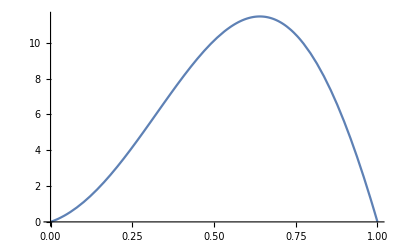

```mathematica
(*Since f is the product of a polynomial and a trigonometric sine function, f is continuous and differentiable everywhere*)
```

```mathematica
f[0]==f[1]
```

True

```mathematica
(*Hence the function satisfies all the conditions of Rolle's theorem*)
```

```mathematica
FindRoot[f'[c]==0,{c,.5}]
```

{c→0.640241}

```mathematica
(*So, the required c is 0.640241*)
```

```mathematica
(*Solution to the question no 2*)
```

```mathematica
Clear[f]
```

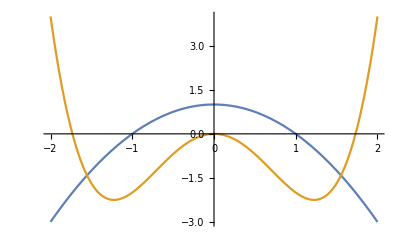

```mathematica
f[x_]=1-x^2;
g[x_]=x^4-3*x^2;
Plot[{f[x],g[x]},{x,-2,2}]
```

```mathematica
intersectionpoints=Solve[f[x]==g[x]]
```

{{x→-ⅈ √(-1+√2)},{x→ⅈ √(-1+√2)},{x→-√(1+√2)},{x→√(1+√2)}}

```mathematica
a=intersectionpoints[[3,1,2]];
b=intersectionpoints[[4,1,2]];
Integrate[f[x]-g[x],{x,a,b}]//N
```

4.48665

```mathematica
(*So, The required area is 4.48665 square units*)
```

```mathematica
(*Solution to the question no 3*)
```

```mathematica
Clear[f,g,a,b,intersectionpoints]
```

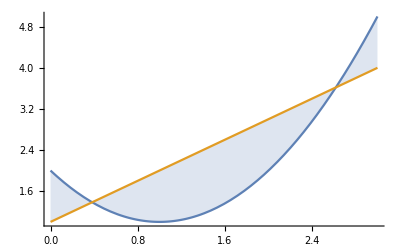

```mathematica
f[x_]=x^2-2*x+2;
g[x_]=x+1;
Plot[{f[x],g[x]},{x,0,3},Filling->{1->{2}}]
```

```mathematica
intersectionpoints=Solve[f[x]==g[x]]
```

{{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

```mathematica
a=intersectionpoints[[1,1,2]];
b=intersectionpoints[[2,1,2]];
Integrate[g[x]-f[x],{x,a,b}]//N
```

1.86339

```mathematica
(*So, the required area is 1.86339 square units*)
```

```mathematica
(*Solution to the question no 4*)
Clear[f,g,a,b,m]
```

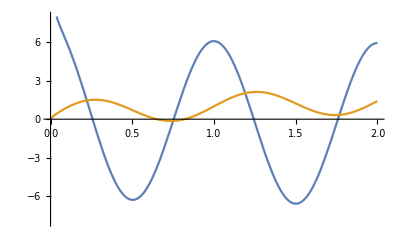

```mathematica
f[x_]=Sqrt[x]+Sin[2*Pi*x];
(*f is continuous and differentiable between 0 and 2*)
a=0;
b=2;
m=(f[b]-f[a])/(b-a);
Plot[{f'[x]-m,f[x]},{x,0,2},PlotRange->{-8,8}]
```

```mathematica
FindRoot[f'[c]==m,{c,{.3,0.8,1.3,1.8}}]
FindRoot[f'[c]==m,{c,.8}]
FindRoot[f'[c]==m,{c,1.3}]
FindRoot[f'[c]==m,{c,1.8}]
```

{c→{0.257071,0.753319,1.24344,1.75836}}

{c→0.753319}

{c→1.24344}

{c→1.75836}

```mathematica
(*So the required values are 0.257071, 0.753319, 1.24344 and 1.75836*)
```

```mathematica
(*Solution to the question no 5*)
```

```mathematica
Clear[a,b,c,f,x,y,z]
```

```mathematica
a[x_,y_,z_]={a1[x,y,z],a2[x,y,z],a3[x,y,z]};
lhs=Curl[Curl[a[x,y,z],{x,y,z}],{x,y,z}];
rhs=Grad[Div[a[x,y,z],{x,y,z}],{x,y,z}]-Laplacian[a[x,y,z],{x,y,z}];lhs==rhs
```

True

```mathematica
Clear[a,lhs,rhs]
a={2,-1,1};
b={1,-3,5};
c={3,-4,4};
Dot[a,Cross[b,c]]
```

10

```mathematica
(*Hence, the vectors are coplaner*)
Dot[a,b]
Dot[a,c]
Dot[b,c]
a.b
```

10

14

35

10

```mathematica
(*Hence, a is perpendicular to b. Consequently the vectors form the sides of a right angle triangle*)
```

```mathematica
Clear[f,a,b,c];
f={3,-2,4};
p1={1,-1,2};
p2={x,y,z};
p=p1-p2
```

{1-x,-1-y,2-z}

```mathematica
moment=Cross[p,f]
```

{-4 y-2 z,2+4 x-3 z,1+2 x+3 y}

```mathematica
(*Solution to the Question no 6*)
A=({{1, 3, 2}, {4, 2, 1}, {0, 3, 2}});
CharacteristicPolynomial[A,λ]
```

1+7 λ+5 λ^2-λ^3

```mathematica
(*Which is the characteristics polynomial of A*)
Eigenvalues[A]
Eigenvectors[A]//MatrixForm
```

{3+√10,-1,3-√10}

(1/6 (4+√10) | 1/3 (1+√10) | 1
1 | -2 | 2
1/6 (4-√10) | 1/3 (1-√10) | 1)

```mathematica
len=Length[A];
eigenvalues=Solve[Det[A-λ*IdentityMatrix[len]]==0,λ]
```

{{λ→-1},{λ→3-√10},{λ→3+√10}}

```mathematica
IdentityMatrix[len]+7*MatrixPower[A,1]+5*MatrixPower[A,2]-MatrixPower[A,3]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
CharacteristicPolynomial[A,x]/x
```

(1+7 x+5 x^2-x^3)/x

```mathematica
MatrixPower[A,2]-5*A-7*IdentityMatrix[len]//MatrixForm
```

(1 | 0 | -1
-8 | 2 | 7
12 | -3 | -10)

```mathematica
(*Solution to the question no 7*)
Clear[A,len,a,b,c]
```

```mathematica
A=({{1, 0, 1}, {2, 1, 0}, {0, -1, 1}});
MatrixRank[A]
```

3

```mathematica
Length[NullSpace[A]]
```

0

```mathematica
(* Rank is 3 and nullity is 0*)
MatrixRank[A]+0==Length[A]
```

True

```mathematica
Inverse[A]//MatrixForm
Det[A]
```

(-1 | 1 | 1
2 | -1 | -2
2 | -1 | -1)

```mathematica
-1
```

```mathematica
(*Solution to the Q no 8*)
Clear[A,b]
```

```mathematica
A=({{-2, 1, -2}, {2, -4, -2}, {1, -4, -2}});b=({{4}, {-4}, {3}});
LinearSolve[A,b]//MatrixForm
```

(-7
-4
3)

```mathematica
Ax=({{4, 1, -2}, {-4, -4, -2}, {3, -4, -2}});Ay=({{-2, 4, -2}, {2, -4, -2}, {1, 3, -2}});Az=({{-2, 1, 4}, {2, -4, -4}, {1, -4, 3}});
{Det[Ax]/Det[A],
Det[Ay]/Det[A],
Det[Az]/Det[A]}
```

{-7,-4,3}

```mathematica
a=({{-2, 1, -2, 4}, {2, -4, -2, -4}, {1, -4, -2, 3}});
RowReduce[a]//MatrixForm
```

(1 | 0 | 0 | -7
0 | 1 | 0 | -4
0 | 0 | 1 | 3)

```mathematica
(*Solution is {-7,-4,3}*)
Inverse[A].b
```

{{-7},{-4},{3}}

```mathematica
(*Solution to the question no 9*)
Clear[lhs,rhs]
```

```mathematica
lhs=(p∨q)∧(p∨r);
rhs=p∨(q∧r);
LogicalExpand[lhs]==LogicalExpand[rhs]
```

True

```mathematica
lhs=p∧(p∨q);
rhs=p;
LogicalExpand[lhs]==LogicalExpand[rhs]
```

True

```mathematica
lhs=p∨(p∧q);
rhs=p;
LogicalExpand[lhs]==LogicalExpand[rhs]
```

True

```mathematica
sum=0;
n=5;
Do[sum=sum+(1/j),{i,1,2 n,2},{j,1,i,2}]
sum
```

2309/315

```mathematica
For[i=1;j=0;t=0,i≤2*n,i=i+2,{j=j+1/i;t=t+j}]
t
```

2309/315

```mathematica
(*Solution to the Q no 10*)

Clear[f]
```

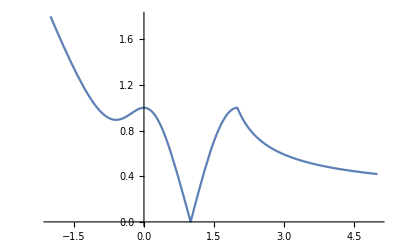

```mathematica
f[x_]:=(1-x^3)/(1+x^2)/;x<1
f[x_]:=Sin[Pi*(x-1)/2]/;1≤x≤2
f[x_]:=1/Log[E(x-1)]/;x>2
Plot[f[x],{x,-2,5}]
```

```mathematica
FindRoot[f[x]==.75,{x,.5}]
FindRoot[f[x]==.75,{x,1.5}]
FindRoot[f[x]==.75,{x,2.5}]
```

{x→0.45541}

{x→1.53989}

{x→2.39561}

```mathematica
(*Solution to the Q no 11*)
```

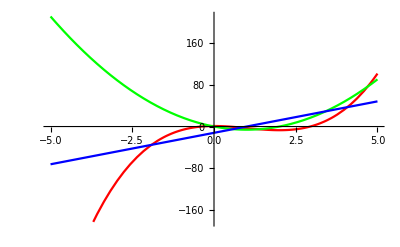

```mathematica
f[x_]=2*x^3-6*x^2+1;
Plot[{f[x],f'[x],f''[x]},{x,-5,5},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]}]
```

```mathematica
Solve[f'[x]==0]
```

{{x→0},{x→2}}

```mathematica
(*which are the critical points*)
```

```mathematica
f'[x]/.x->-1
```

18

```mathematica
f'[x]/.x->1
```

-6

```mathematica
f'[x]/.x->3
```

18

```mathematica
(*Hence, f is increasing on (-∞,0) and (2,∞) and decreasing on (0,2)*)
```

```mathematica
Solve[f''[x]==0]
```

{{x→1}}

```mathematica
(*which is the point of inflection*)
```

```mathematica
f''[x]/.x->0
```

-12

```mathematica
f''[x]/.x->2
```

12

```mathematica
(* f is concave up on (1,∞) and down on (-∞,1)*)
```

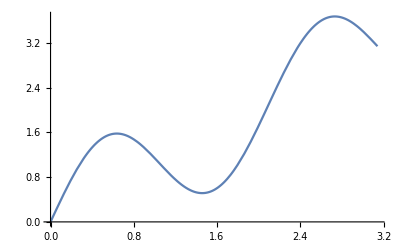

```mathematica
(*Solution to the Q no 12*)
f[x_]=x+Sin[3*x];
Plot[f[x],{x,0,Pi}]
```

```mathematica
cri=FindRoot[f'[x]==0,{x,{.5,1.5,2.7}}]
```

{x→{0.636878,1.45752,2.73127}}

```mathematica
f'[x]/.x->0.5
f'[x]/.x->1.3
f'[x]/.x->2.6
f'[x]/.x->2.8
```

1.21221

-1.1778

1.16187

-0.557866

```mathematica
(*f in increasing on(0,0.636878) and(1.45752,2.731272) and decreasing on (0.63687,1.45751) and (2.73127,3.14159)*)
inf=FindRoot[f''[x]==0,{x,{0,1,2,3}}]
```

{x→{0.,1.0472,2.0944,3.14159}}

```mathematica
f''[x]/.x->.5
f''[x]/.x->1.5
f''[x]/.x->2.6
```

-8.97745

8.79777

-8.98689

```mathematica
(*f is concave up on (1.0472,2.0944) and down  on (0,1.0472) and (2.0944,3.14159)*)
```

```mathematica
FindMinimum[f[x],{x,1.5}]
```

{0.514708,{x→1.45752}}

```mathematica
FindMaximum[f[x],{x,1}]
FindMaximum[f[x],{x,3.5}]
```

{1.57969,{x→0.636878}}

{3.67408,{x→2.73127}}

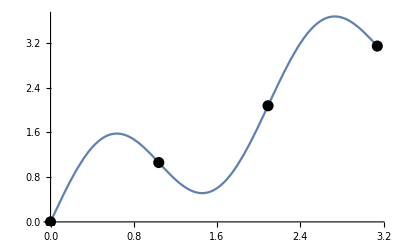

```mathematica
curve=Plot[f[x],{x,0,Pi}];
p1=Graphics[{PointSize[0.02],Point[{1.04,f[1.04]}]}];
p2=Graphics[{PointSize[0.02],Point[{2.09,f[2.09]}]}];
p3=Graphics[{PointSize[0.02],Point[{3.14,f[3.14]}]}];
p4=Graphics[{PointSize[0.02],Point[{0,f[0]}]}];
Show[curve,p1,p2,p3,p4]
```

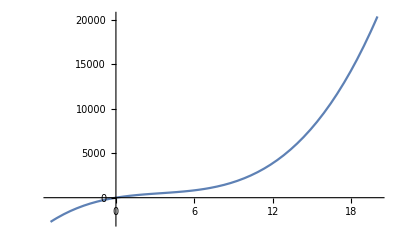

```mathematica
(*solution to the Q no 13*)
f[x_]=240*x-41*x^2+4*x^3;
Plot[f[x],{x,-5,20}]
```

```mathematica
cri=NSolve[f'[x]==0]
```

{{x→3.41667-2.88555 ⅈ},{x→3.41667+2.88555 ⅈ}}

```mathematica
(*there is no real critical point for f. thus, the function is increasing on (-∞,∞)*)
```

```mathematica
inf=NSolve[f''[x]==0]
```

{{x→3.41667}}

```mathematica
f''[x]/.x->2
f''[x]/.x->4
```

-34

14

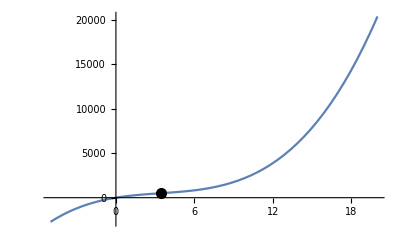

```mathematica
(*So, f is concave up on (3.41667,∞) and down on (-∞,3.41667)*)
curve=Plot[f[x],{x,-5,20}];
p1=Graphics[{PointSize[0.02],Point[{3.41667,f[3.41667]}]}];
Show[curve,p1]
```

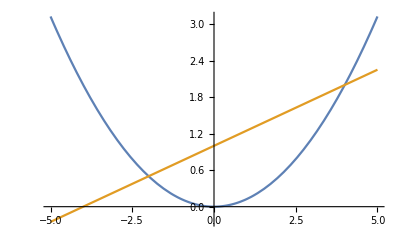

```mathematica
(*Solution to the Q no 14*)
f[y_]=y^2/8;
g[y_]=(y+4)/4;
Plot[{f[y],g[y]},{y,-5,5}]
```

```mathematica
intersectionpoints=Solve[f[y]==g[y]]
```

{{y→-2},{y→4}}

```mathematica
a=intersectionpoints[[1,1,2]];
b=intersectionpoints[[2,1,2]];
Integrate[g[y]-f[y],{y,a,b}]
```

9/2

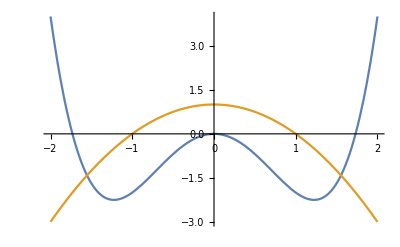

{{x→-ⅈ √(-1+√2)},{x→ⅈ √(-1+√2)},{x→-√(1+√2)},{x→√(1+√2)}}

4.48665

```mathematica
f[x_]=1-x^2;
g[x_]=x^4-3*x^2;
Plot[{g[x],f[x]},{x,-2,2}]
isp=Solve[f[x]==g[x]]
a=isp[[3,1,2]];
b=isp[[4,1,2]];
Integrate[f[x]-g[x],{x,a,b}]//N
```

```mathematica
Clear[f,g,a,b]
```

```mathematica
f[x_,y_]=5*x^2+5*y^2;
g[x_,y_]=6-7*x^2-y^2;
ContourPlot3D[{z==f[x,y],z==g[x,y]},{x,-5,5},{y,-5,5},{z,-5,6}]
```

-Graphics3D-

```mathematica
s1=Solve[f[x,y]==g[x,y],y]
```

{{y→-√(1-2 x^2)},{y→√(1-2 x^2)}}

```mathematica
s2=Solve[s1[[1,1,2]]==0,x]
```

{{x→-1/(√2)},{x→1/(√2)}}

```mathematica
Integrate[Integrate[Integrate[1,{z,g[x,y],f[x,y]}],{y,Sqrt[1-2*x^2],-Sqrt[1-2*x^2]}],{x,-1/Sqrt[2],1/Sqrt[2]}]//N
```

6.66432

```mathematica
∫_(-1/Sqrt[2])^(1/Sqrt[2]) ∫_(-Sqrt[1-2*x^2])^Sqrt[1-2*x^2] ∫_f[x,y]^g[x,y] ⅆzⅆyⅆx//N
```

6.66432

```mathematica
(*Solution to the Q no 15*)
Clear[a,b,c,h,g,f,x,y,X,Y]
p:=32*x^2+52*x*y-7*y^2-64*x-52*y-148
a=32;b=-7;c=-148;
h=26;g=-32;f=-26;
d1=Det[({{a, h, g}, {h, b, f}, {g, f, c}})]
d2=a*b-h^2
d3=a+b
```

162000

-900

25

```mathematica
α=(f h-b g)/d2;
β=(g h-a f)/d2;
θ=(1/2)ArcTan[2*h/(a-b)];
P=Expand[p/.x->X*Cos[θ]-Y*Sin[θ]+1/.y->X*Sin[θ]+Y*Cos[θ]//Simplify]
```

-180+45 X^2-20 Y^2

```mathematica
L1=(P+180)/180//Simplify
```

X^2/4-Y^2/9

```mathematica
var=Expand[Solve[x==X*Cos[θ]-Y*Sin[θ]+1&&y==X*Sin[θ]+Y*Cos[θ],{X,Y}]]//N
```

{{X→-0.894427+0.894427 x+0.447214 y,Y→0.447214-0.447214 x+0.894427 y}}

```mathematica
X1=var[[1,1,2]];
Y1=var[[1,2,2]];
A=2;
B=3;
e=Sqrt[1-(A^2/B^2)];
p1=Solve[X1==A*e&&Y1==0,{x,y}]
p2=Solve[X1==-A*e&&Y1==0,{x,y}]
Solve[X1==0,y]//Expand
Solve[Y1==0,y]//Expand
Solve[X1==A*e,y]
Solve[X1==-A*e,y]
Solve[X1==A/e,y]
Solve[X1==-A/e,y]
```

{{x→2.33333,y→0.666667}}

{{x→-0.333333,y→-0.666667}}

{{y→2.-2. x}}

{{y→-0.5+0.5 x}}

{{y→2.23607 (2.38514-0.894427 x)}}

{{y→2.23607 (-0.596285-0.894427 x)}}

{{y→2.23607 (3.57771-0.894427 x)}}

{{y→2.23607 (-1.78885-0.894427 x)}}

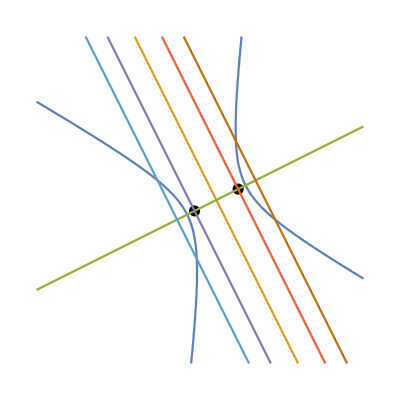

```mathematica
k=10;
bb=Graphics[{PointSize[0.02],{Point[{p1[[1,1,2]],p1[[1,2,2]]}],Point[{p2[[1,1,2]],p2[[1,2,2]]}]}}];
dd=ContourPlot[{p==0,X1==0,Y1==0,X1==A*e,X1==-A*e,X1==A/e,X1==-A/e},{x,-k,k},{y,-k,k}];
Show[bb,dd]
```

```mathematica
(*Solution to the Q no 16*)
p:=λ*x^2+4*x*y+y^2-4*x-2*y-3;
a=λ;b=1;c=-3;
h=2;g=-2;f=-1;
Solve[Det[({{a, h, g}, {h, b, f}, {g, f, c}})]==0,λ]
```

{{λ→4}}

```mathematica
Factor[p/.λ->4]
```

(-3+2 x+y) (1+2 x+y)

```mathematica
(*Solution to the Q no 17*)
x1=3;y1=8;z1=3;
l1=3;m1=-1;n1=-1;
x2=-3;y2=-7;z2=6;
l2=-3;m2=2;n2=4;
ang=ArcSin[Sqrt[(m1*n2-n1*m2)^2+(n1*l2-l1*n2)^2+(l1*m2-m1*l2)^2]];
l=(m1*n2-n1*m2)/Sin[ang];
m=(n1*l2-n2*l1)/Sin[ang];
n=(l1*m2-m1*l2)/Sin[ang];
SD=l*(x2-x1)+m*(y2-y1)+n*(z2-z1)//Simplify
A1=({{x-x1, y-y1, z-z1}, {l1, m1, n1}, {l, m, n}});
SD1=Det[A1]//Simplify;
A2=({{x-x1, y-y1, z-z1}, {l2, m2, n2}, {l, m, n}});
SD2=Det[A2]//Simplify;
SD1==0
SD2==0
```

78 √(2/47)

-(-179+12 x+7 y+29 z)/(√94)==0

(-227+42 x+y+31 z)/(√94)==0

```mathematica
Clear[f,m,x,y]
f[x_]=x^2-2*x+5;
m=D[f[x],x]/.x->2
y-3==m*(x-2)//Simplify
y-3==-(1/m)*(x-2)//Simplify
```

2

2 x==1+y

x+2 y==8

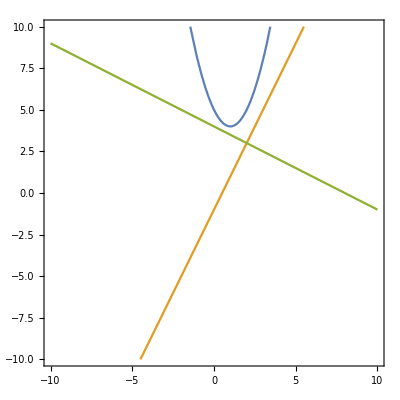

```mathematica
ContourPlot[{f[x]==y,2*x==1+y,x+2y==8},{x,10,-10},{y,-10,10}]
```